# Math transformer for the AP-M1-CBS module

Just another code, based on the original toy code thingy.

This is a printout from an explorative notebook of SvenK at 2019-12-04 to explore the feasibility of a "formula translator" for analog computers, without making use of anything else then a standard computer algebra system (namely Wolfram Mathematica 12). The code is written with the "Model-1" analog computer in mind (produced by analogparadigm.com)

## Section 1) Transforming simple arithmetic expressions

```mathematica
ClearAll["Global`*"]
```

```mathematica
ElementaryParts= {
Summer,Multiplier,Integrator,  (* elementary parts *)
PlusOne,MinusOne, (* Logic Levels *)
Variable     (* helper parts *)
};
devName = Symbol[ToString@#<>"Dev"]&; (* map part -> device name *)
undev=Symbol@StringTrim[ToString@#,"Dev"]&; (* map device -> part name *)
(* short names only for printing *)
shortName =#//.{Summer -> Σ, Multiplier -> Π, Integrator-> "∫",PlusOne-> 𝟙,MinusOne-> -𝟙}&;
mmaShorts=#//.{Plus-> Σ,Times->Π}&;
subby=#//.{x_[{a_,b_},{a0_,b0_}]-> Subscript[x, a0,b0][a,b]}&;
(* By definition, any part such as Summer, Multiplier, has
as first element the actual children and as last one the multiplicities.
See the backward rules for the interpretation *)
Children=First;Multiplicities=Last;
ElementaryRules[mma_,analog_,mmaMultiply_:Times]:={
(* bring to canonical forms *)
mma[a_,b_]-> analog[{a,b},{1,1}],
(* the actual replacement *)
mma[mmaMultiply[a0_?NumberQ, a_], mmaMultiply[b0_?NumberQ, b_]]-> analog[{a,b},{a0,b0}],
(* Cannot create numbers from nothing: *)
analog[{a_?NumberQ,b_},{a0_,b0_}]-> analog[{PlusOne,b},{a*a0,b0}]
}
AnalogParadigmRules=Join[{
(* Special rules for Times *)
Times[a0_?NumberQ, a_,b_]-> Multiplier[{a,b},{a0,1}],
Times[a0_?NumberQ, a_]-> Multiplier[{a,PlusOne},{a0,1}],
Integrate[x_,t]->Integrator[x] (* x must be formally x[t] else ∫ evaluates *)
},
ElementaryRules[Plus,Summer],
ElementaryRules[Times,Multiplier],
{
(* Special rules for Minus in Sums *)
 Summer[{s1_,Multiplier[{m1_,PlusOne},{md1_,md2_}]},{sd1_,sd2_}]-> 
Summer[{s1,m1},{sd1,md1*md2*sd2}],
(* First@Summer should be orderless :-/ *)
Summer[{Multiplier[{m1_,PlusOne},{md1_,md2_}],s2_},{sd1_,sd2_}]-> 
Summer[{m1,s2},{md1*md2*sd1,sd2}]
}
];
BackwardRule[analogPart_,mma_,mmaMultiply_:Times]:=
analogPart[{a_,b_},{a0_,b0_}]->mma[ mmaMultiply[a0,a],mmaMultiply[b0,b]];
BackwardRules={
BackwardRule[Summer,Plus],
BackwardRule[Multiplier, Times],
PlusOne-> +1, MinusOne-> -1
};
Terms2AnalogParadigm[expr_]:=expr//.Dispatch@AnalogParadigmRules
AnalogParadigm2Terms[expr_]:=expr//.Dispatch@BackwardRules
```

```mathematica
tests = {a+b,a*b,a+15+b+17,a*b 3*c*d,a*(c+d)13+(f*(g+h)),
a-b,a-5b,a-15-b-c-d};
Grid[
 {{"MMA", "Analog","Backwards check","Correct?"}}~Join~
Table[Module[{
ana=Terms2AnalogParadigm@mma,
back=AnalogParadigm2Terms@Terms2AnalogParadigm@mma
},{mmaShorts@mma,subby@shortName@ana,back,SameQ[mma,back]}],{mma,tests}],
Dividers->All]//TraditionalForm
```

MMA | Analog | Backwards check | Correct?
Σ(a,b) | Σ_(1,1)(a,b) | a+b | True
Π(a,b) | Π_(1,1)(a,b) | a b | True
Σ(32,a,b) | Σ_(32,1)(𝟙,Σ_(1,1)(a,b)) | a+b+32 | True
Π(3,a,b,c,d) | Π_(3,1)(a,Π_(1,1)(b,Π_(1,1)(c,d))) | 3 a b c d | True
Σ(Π(13,a,Σ(c,d)),Π(f,Σ(g,h))) | Σ_(1,1)(Π_(13,1)(a,Σ_(1,1)(c,d)),Π_(1,1)(f,Σ_(1,1)(g,h))) | 13 a (c+d)+f (g+h) | True
Σ(a,Π(-1,b)) | Σ_(1,-1)(a,b) | a-b | True
Σ(a,Π(-5,b)) | Σ_(1,-5)(a,b) | a-5 b | True
Σ(-15,a,Π(-1,b),Π(-1,c),Π(-1,d)) | Σ_(-15,1)(𝟙,Σ_(1,1)(a,Σ_(-1,1)(b,Σ_(-1,-1)(c,d)))) | a-b-c-d-15 | True

```mathematica
EvenMoreTerms2AnalogParadigm = {
Plus[a_,Times[-1,b]]-> Substractor[a,b], (* a-b == a+(-b) in MMA *)
InverseFunction->Inverser,
Times[a_,Power[b_,-1]]-> Inverser[Multiplier[a,b]] ,(* a/b == a*(1/b) in MMA *)
Sqrt-> SquareRooter,
Power[1,t]->OneOverTime,
Power[x_,n_]-> IntegratePolynomials, (* ... *)
Abs->Abser, Min->LimitDown,Max->LimitUp, etc-> pp
};
```

```mathematica
(* NB: This can only recognize "semi-explicit" equations of type y==f(y,…,x).
You should prepare any equation with Solve[eqn,{y}] or similar *)
Equation2AnalogParadigm[expr_]:=ReplaceAll[expr,
Equal[a_Symbol,b_]-> Variable[a,b]];
Mathematica2AnalogParadigm = Equation2AnalogParadigm@*Terms2AnalogParadigm;
```

Here is an example of how a simple expression with some constants (numbers) and input variables (a,b,c,d) transforms:

```mathematica
testEquation = f==a(c 5+d)+4a f+15;
analogTestEq=Mathematica2AnalogParadigm[testEquation]
```

Variable[f,Summer[{PlusOne,Summer[{Multiplier[{a,Summer[{c,d},{5,1}]},{1,1}],Multiplier[{a,f},{4,1}]},{1,1}]},{15,1}]]

#### Giving unique names to each Adder, Multiplier, ...

We now transform the tree structure of an expression in a way that each primitive operation (called “part”) is uniquly marked (which then allows to identify it with a physical “device”). For simplicity, the “devices” are just enumerated (they would be most likely given names when written out in a HDL by humans, or some “temporary variable” names when being used in a code generation as typically done for FORTRAN/C).

```mathematica
(* aexpr is the output of Mathematica2AnalogParadigm[some equation(s)] *)
exprParts[aexpr_] := Cases[indent@aexpr, Blank@#, Infinity]&/@ElementaryParts;
exprDevsWithArgs[aexpr_]:=MapIndexed[Apply[devName[Head@#1][Last@#2],#1]&, exprParts@aexpr,{2}]
(* args still parts, not devs *)
exprPart2DevsWArgs[aexpr_] := Replace[Transpose@{Flatten@exprParts@aexpr,Flatten@exprDevsWithArgs@aexpr} ,
List->Rule,{2},Heads->True];
uniqueAnalogExpr[aexpr_]:=aexpr//.exprPart2DevsWArgs[aexpr];
beautyDev=#//.Map[#[n_]:> Symbol[ToString@#<>ToString@n]&,devName~Map~ElementaryParts]&;
subbyDev= #//.Map[#[n_]:> ToString@shortName@undev@#<>ToString@n  devName~Map~ElementaryParts]&;
```

The following table basically shows the mapping between “unnamed” or “anonymous” evaluation of operations (left column) and unique names of their physical manifestation. Compare also the subsequent tree of the unnamed AnalogParadigm primitives with the on with named ones:

Analog primtives | Physical devices
Σ_(5,1)[c,d] | SummerDev[1]_(5,1)[c,d]
Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]] | SummerDev[2]_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]
Σ_(15,1)[𝟙,Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]] | SummerDev[3]_(15,1)[𝟙,Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]]
Π_(1,1)[a,Σ_(5,1)[c,d]] | MultiplierDev[1]_(1,1)[a,Σ_(5,1)[c,d]]
Π_(4,1)[a,f] | MultiplierDev[2]_(4,1)[a,f]
Variable[f,Σ_(15,1)[𝟙,Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]]] | VariableDev[1][f,Σ_(15,1)[𝟙,Σ_(1,1)[Π_(1,1)[a,Σ_(5,1)[c,d]],Π_(4,1)[a,f]]]]

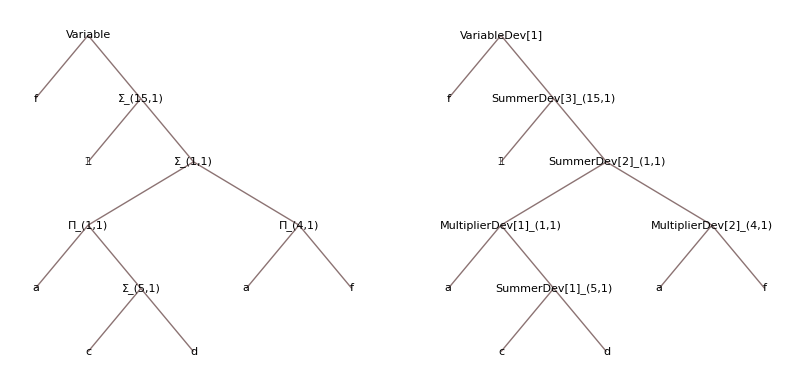

```mathematica
TableForm[ subby@shortName@exprPart2DevsWArgs[analogTestEq]/.Rule->List,TableHeadings-> {None,{"Analog primtives","Physical devices"}}]
GraphicsGrid[{TreeForm@shortName@subby@#@Mathematica2AnalogParadigm@testEquation&/@{Identity,uniqueAnalogExpr}}]
```

#### Identify the wiring

```mathematica
allSubtrees[aexpr_]:=Flatten[Cases[indent@uniqueAnalogExpr@aexpr,#[_][__],Infinity, Heads->True]&/@devName/@ElementaryParts];
edgeList[n_]:=MapIndexed[{
If[LeafCount@Children@#>1,(Head@#)[outJack],#],(Head@n)[inJack[First@#2]] }&,List@@n];
wiring[aexpr_]:=Flatten[edgeList/@allSubtrees@aexpr, 1];
wiringWithoutJacks[aexpr_]:=wiring@aexpr//.{x_[inJack[_]]-> x,x_[outJack]-> x};
```

This code is not great but simple enough to demonstrate how to identify variables across the tree (which share a single value and therefore can/should be wired together). Interestingly, the tree is now no more a tree:

```mathematica
First@allSubtrees[analogTestEq]
```

SummerDev[1][{c,d},{5,1}]

```mathematica
wiringWithoutJacks[analogTestEq]//TableForm;
wiring[analogTestEq]//TableForm
TreePlot[wiringWithoutJacks@analogTestEq/.{a_,b_}->(a->b),
Automatic, OutputVariableDev[1],(* optional line to define "root" element *) 
PlotTheme->"ClassicLabeled"]
```

outJack | SummerDev[1][inJack[1]]
outJack | SummerDev[1][inJack[2]]
outJack | SummerDev[2][inJack[1]]
outJack | SummerDev[2][inJack[2]]
outJack | SummerDev[3][inJack[1]]
outJack | SummerDev[3][inJack[2]]
outJack | MultiplierDev[1][inJack[1]]
outJack | MultiplierDev[1][inJack[2]]
outJack | MultiplierDev[2][inJack[1]]
outJack | MultiplierDev[2][inJack[2]]
f | VariableDev[1][inJack[1]]
SummerDev[3][outJack] | VariableDev[1][inJack[2]]

TreePlot::rind: Argument OutputVariableDev[1] at position 3 is not a valid vertex.

TreePlot[{List→SummerDev[1],List→SummerDev[1],List→SummerDev[2],List→SummerDev[2],List→SummerDev[3],List→SummerDev[3],List→MultiplierDev[1],List→MultiplierDev[1],List→MultiplierDev[2],List→MultiplierDev[2],f→VariableDev[1],SummerDev[3]→VariableDev[1]},Automatic,OutputVariableDev[1],PlotTheme→ClassicLabeled]

#### Print a wiring list

```mathematica
AnalogParadigmCounter={ 
Adder-> 1./8., Multiplier-> 1./8., Integrator-> 1./4.,
Divider->1./2.,  InputConstant-> 1./8., OutputVariable-> 1./4.};
AnalogParadigmDev2Module = {
Adder -> "SUM8", Multiplier-> "MLT8", Integrator->"INT4",
 Divider-> "MSD2"(*missing mode*),InputConstant-> "PT8",
 OutputVariable-> "XIBNC" };
 (* beautifying: Write device addresses more compact/OOP-like *)
IObeautify[naming_]:=naming/.OutputVariableDev[n_][inout_]:> OutputVariableDev[n]; 
beautify[naming_]:=IObeautify@naming \
/.Map[#[n_]:> Symbol[ToString@#<>ToString@n]&,devName~Map~AnalogParadigmParts] \
/. {x_[outJack]:> ToString@x<>".output",x_[inJack[n_]]:> StringForm["``.input(``)",x,n]}
Equation2Wiring[analogEquations_,mmaEquations_:None]:=(
Print[Style["Wiring and component list", 18, Bold, Red]];
Print["To implement the expression:"];
Print["  ", TraditionalForm@If[mmaEquations~SameQ~None,analogEquations,mmaEquations]];
Print["Required Parts:"~Style~Bold];
Print["  Basic arithmetic units: ", StringForm@@({"`` x ``"}~Join~#)&/@  Transpose@{Length/@exprParts[analogEquations],AnalogParadigmParts}];
Print["  Model-1 modules: ",StringForm@@({"`` x ``"}~Join~#)&/@ ({Ceiling[Last@#*First@#/.AnalogParadigmCounter],First@#/.AnalogParadigmDev2Module}&/@Transpose@{AnalogParadigmParts,Length/@exprParts[analogEquations]})];
Print["Wiring:"~Style~Bold];
Scan[Print[StringForm["  `` -> ``", beautify@First@#, beautify@Last@#]]&,wiring[analogEquations]]
)
```

Here’s the written-out part and wiring plan for the test equation:

```mathematica
Equation2Wiring[analogTestEq,testEquation]
```

Wiring and component list

To implement the expression:

f==a (b+5 c+d)+4 a

Required Parts:

Basic arithmetic units: {2 x Adder,3 x Multiplier,0 x Integrator,0 x InputConstant,1 x OutputVariable}

Model-1 modules: {1 x SUM8,1 x MLT8,0 x INT4,0 x PT8,1 x XIBNC}

Wiring:

b -> AdderDev1.input(1)

MultiplierDev2.output -> AdderDev1.input(2)

d -> AdderDev1.input(3)

MultiplierDev1.output -> AdderDev2.input(1)

MultiplierDev3.output -> AdderDev2.input(2)

4 -> MultiplierDev1.input(1)

a -> MultiplierDev1.input(2)

5 -> MultiplierDev2.input(1)

c -> MultiplierDev2.input(2)

a -> MultiplierDev3.input(1)

AdderDev1.output -> MultiplierDev3.input(2)

f -> OutputVariableDev1

AdderDev2.output -> OutputVariableDev1

#### Review of the wiring

What a few lines of code can do:

Determine the material needed, tell about the input and output jacks to be connected.
Particular shortcomings:

It didn't enumerate Model-1 modules, i.e. did not take them into account at the wiring output.
General shortcomings:

The generated circuit is certainly not realistic. It is not optimized in terms of using only a minimal amount of hardware.

## Section 2) Transforming simple differential equations

```mathematica
lorentz={ 
D[x[t],t]==σ(y[t]-x[t]),
D[y[t],t]==x[t](ρ-z[t])-y[t],
D[z[t],t]==x [t]y[t] - β z[t]
};
params = { σ-> 10, β->2.6667,ρ->28};
lorentz//TableForm//TraditionalForm
```

x'(t)==σ (y(t)-x(t))
y'(t)==x(t) (ρ-z(t))-y(t)
z'(t)==x(t) y(t)-β z(t)

```mathematica
IntegrateEquation[x_==y_]:=Integrate[x,t]==Integrate[y,t]
integralLorentz=IntegrateEquation/@lorentz/.params//N;
integralLorentz//TableForm//TraditionalForm
```

x(t)==10. ∫(y(t)-x(t))ⅆt
y(t)==∫(x(t) (28-z(t))-y(t))ⅆt
z(t)==∫(x(t) y(t)-2.6667 z(t))ⅆt

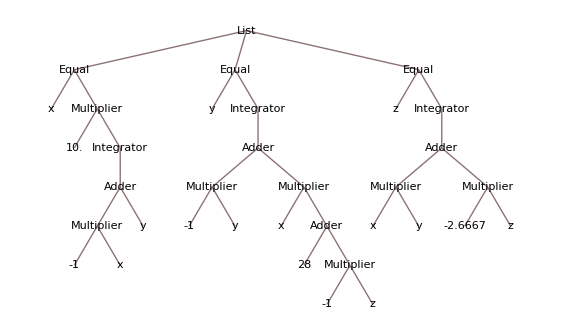

```mathematica
analogLorentz=Mathematica2AnalogParadigm[integralLorentz]/.{x[t]->x,y[t]->y,z[t]->z};  (* removing explicit time dependency *)
analogLorentz//TreeForm
```

#### Wiring the Lorentz attractor ODE (naively...)

```mathematica
Graph[wiringWithoutJacks[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"ClassicLabeled",GraphLayout->"GravityEmbedding"]
```

-Graphics-

It’s hard to tell something from these graphs, the layouting (and labeling) is not fine-tuned. The previous one shows the wiring (ignoring the jacks at the devices), while the next ones compares how the jack-aware connection graph looks like (i.e. the actual “isovoltage” lines, if you want).

```mathematica
GraphicsGrid[{{
Graph[wiringWithoutJacks[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"LargeGraph",GraphLayout->"SpringEmbedding"],
Graph[wiring[analogLorentz]/.{a_,b_}->(a->b), PlotTheme->"LargeGraph",GraphLayout->"SpringEmbedding"]
}},ImageSize->Large]
```

-Graphics-

```mathematica
Equation2Wiring[analogLorentz,TableForm@integralLorentz]
```

Wiring and component list

To implement the expression:

x(t)==10. ∫(y(t)-x(t))ⅆt
y(t)==∫(x(t) (28-z(t))-y(t))ⅆt
z(t)==∫(x(t) y(t)-2.6667 z(t))ⅆt

Required Parts:

Basic arithmetic units: {4 x Adder,7 x Multiplier,3 x Integrator,0 x InputConstant,0 x OutputVariable}

Model-1 modules: {1 x SUM8,1 x MLT8,1 x INT4,0 x PT8,0 x XIBNC}

Wiring:

MultiplierDev1.output -> AdderDev1.input(1)

y -> AdderDev1.input(2)

28 -> AdderDev2.input(1)

MultiplierDev4.output -> AdderDev2.input(2)

MultiplierDev3.output -> AdderDev3.input(1)

MultiplierDev5.output -> AdderDev3.input(2)

MultiplierDev6.output -> AdderDev4.input(1)

MultiplierDev7.output -> AdderDev4.input(2)

- continued -

-1 -> MultiplierDev1.input(1)

x -> MultiplierDev1.input(2)

10. -> MultiplierDev2.input(1)

IntegratorDev1.output -> MultiplierDev2.input(2)

-1 -> MultiplierDev3.input(1)

y -> MultiplierDev3.input(2)

-1 -> MultiplierDev4.input(1)

z -> MultiplierDev4.input(2)

x -> MultiplierDev5.input(1)

AdderDev2.output -> MultiplierDev5.input(2)

x -> MultiplierDev6.input(1)

y -> MultiplierDev6.input(2)

-2.6667 -> MultiplierDev7.input(1)

z -> MultiplierDev7.input(2)

AdderDev1.output -> IntegratorDev1.input(1)

AdderDev3.output -> IntegratorDev2.input(1)

AdderDev4.output -> IntegratorDev3.input(1)

#### Review of the Lorentz attractor wiring

The generated circuit differs a lot from the one proposed by Bernd in his books. An obvious reasons (telling from the equations itself) is that no efforts have been made to check any bounds (scaling of voltages/logic levels, probably introducing helper quantities). Furthermore, as said in the introductory example above, there is a number of general shortcomings, such as that we don’t enumerate Model-1 modules, i.e. don’t take them into account at the wiring output.